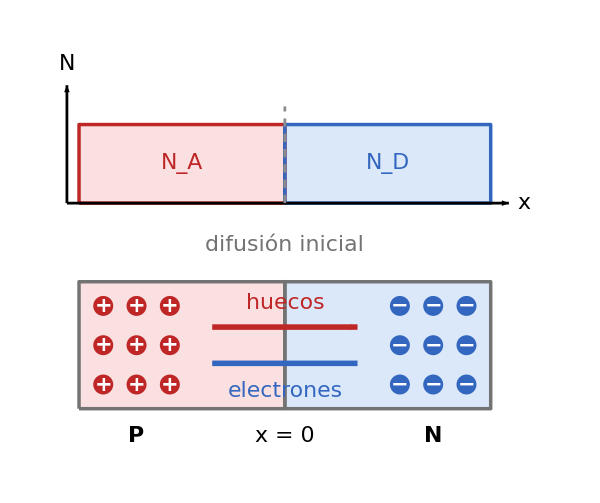

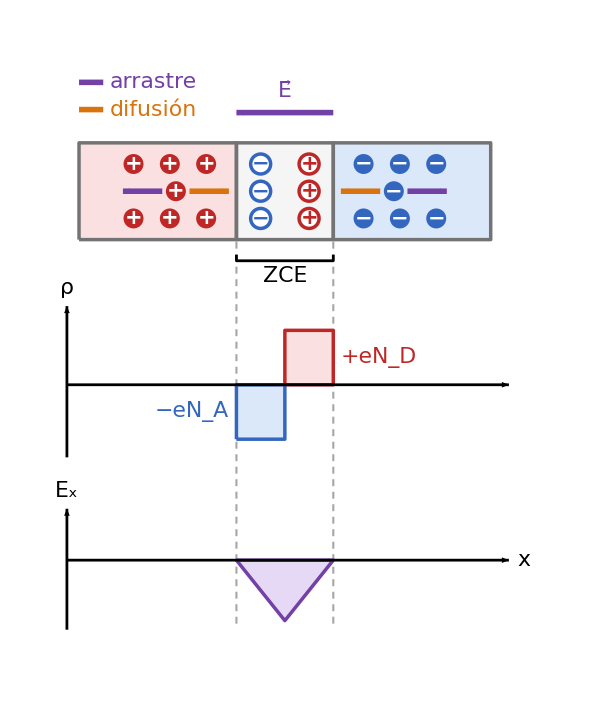

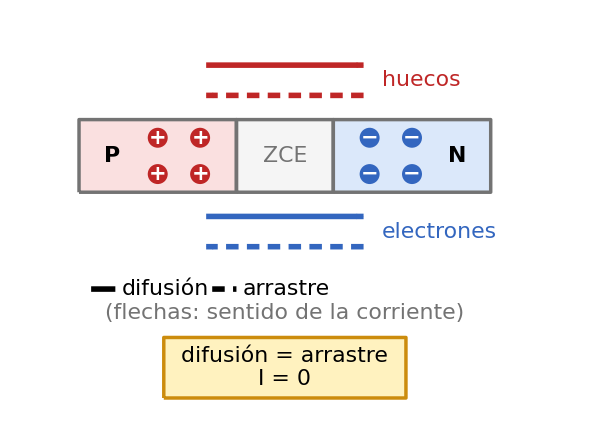

```mathematica
{diagramaPNb, diagramaPNc, diagramaPNd} = Module[
  {fs, dopA, dopD, mx, Wz, xp, xn, cx, uMax, X,
   cAzul, cAzulB, cRojo, cRojoF, cVio, cVioF, cNar, cGris, cOro, cOroB,
   ins, insI, flecha, carga, ion, caja, eje, ejeV, zonas,
   yb, hA, hD, yE, hE, yR, hAr, hDr, uc, g1, g2, g3},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                  (* tamaño de fuente único para todo el gráfico *)
  {dopA, dopD} = {1., 1.};  (* dopados relativos N_A y N_D: cualquier valor > 0 (mejor entre 1/3 y 3) *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo = RGBColor[0.75, 0.15, 0.15];  cRojoF = RGBColor[0.98, 0.88, 0.88];
  cVio  = RGBColor[0.45, 0.25, 0.65];  cVioF  = RGBColor[0.90, 0.85, 0.96];
  cNar  = RGBColor[0.85, 0.45, 0.05];  cGris  = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Geometría común (u = posición respecto a la unión, x = 0) ---------- *)
  mx = Max[dopA, dopD];
  Wz = 3.2;                        (* anchura total de la ZCE (esquemática) *)
  xp = Wz dopD/(dopA + dopD);      (* penetración de la ZCE en el lado P *)
  xn = Wz dopA/(dopA + dopD);      (* penetración de la ZCE en el lado N *)
  cx = 7.6;  uMax = 6.8;
  X[u_] := cx + u;

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  flecha[p1_, p2_, col_, dash_: {}] :=
    {col, AbsoluteThickness[4], AbsoluteDashing[dash], Arrowheads[0.03], Arrow[{p1, p2}]};
  carga[pos_, signo_, col_] :=
    {col, Disk[pos, 0.33], Text[Style[signo, Round[0.95 fs], Bold, White], pos]};
  ion[pos_, signo_, col_] :=
    {White, Disk[pos, 0.33], col, AbsoluteThickness[2.5], Circle[pos, 0.33],
     Text[Style[signo, Round[0.95 fs], Bold, col], pos]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  eje[u0_, u1_, y_] :=
    {Black, AbsoluteThickness[2], Arrowheads[0.025], Arrow[{{X[u0], y}, {X[u1], y}}]};
  ejeV[u_, y0_, y1_] :=
    {Black, AbsoluteThickness[2], Arrowheads[0.025], Arrow[{{X[u], y0}, {X[u], y1}}]};
  zonas[y0_, y1_, conZCE_] := {
    {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{X[-uMax], y0}, {X[If[conZCE, -xp, 0]], y1}]},
    {cAzul, EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{X[If[conZCE, xn, 0]], y0}, {X[uMax], y1}]},
    If[conZCE,
     {GrayLevel[0.96], EdgeForm[{AbsoluteThickness[2.5], cGris, AbsoluteDashing[{7, 5}]}],
      Rectangle[{X[-xp], y0}, {X[xn], y1}]},
     {}]};

  (* ===== Figura b: perfil de dopado y difusión inicial ===== *)
  yb = 10.8;  hA = 2.6 dopA/mx;  hD = 2.6 dopD/mx;
  g1 = Graphics[{
     (* perfil de dopado ideal *)
     {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cRojo}],
      Rectangle[{X[-uMax], yb}, {X[0], yb + hA}]},
     {cAzul, EdgeForm[{AbsoluteThickness[2.5], cAzulB}],
      Rectangle[{X[0], yb}, {X[uMax], yb + hD}]},
     ins[Row[{Subscript["N", "A"]}], {X[-3.4], yb + hA/2}, cRojo],
     ins[Row[{Subscript["N", "D"]}], {X[3.4], yb + hD/2}, cAzulB],
     eje[-7.2, 7.4, yb], ejeV[-7.2, yb, yb + 3.9],
     ins[Style["x", Italic], {X[7.9], yb}],
     ins[Style["N", Italic], {X[-7.2], yb + 4.6}],
     {GrayLevel[0.55], AbsoluteThickness[2], AbsoluteDashing[{6, 5}],
      Line[{{cx, yb}, {cx, yb + 3.2}}]},

     (* barra P | N con portadores y difusión inicial *)
     zonas[4.0, 8.2, False],
     Table[carga[{X[u], y}, "+", cRojo], {u, {-6.0, -4.9, -3.8}}, {y, {4.8, 6.1, 7.4}}],
     Table[carga[{X[u], y}, "−", cAzulB], {u, {3.8, 4.9, 6.0}}, {y, {4.8, 6.1, 7.4}}],
     flecha[{X[-2.4], 6.7}, {X[2.4], 6.7}, cRojo],
     flecha[{X[2.4], 5.5}, {X[-2.4], 5.5}, cAzulB],
     ins["huecos", {cx, 7.5}, cRojo],
     ins["electrones", {cx, 4.6}, cAzulB],
     ins["difusión inicial", {cx, 9.4}, cGris],
     ins[Style["P", Bold], {X[-4.9], 3.1}],
     ins[Style["N", Bold], {X[4.9], 3.1}],
     ins[Row[{Style["x", Italic], " = 0"}], {cx, 3.1}]
    },
    ImageSize -> 600, PlotRange -> {{0, 16.2}, {2.4, 16.0}},
    PlotRangePadding -> None, AspectRatio -> 13.6/16.2, Background -> White];

  (* ===== Figura c: carga fija, campo interno y fuerzas ===== *)
  yE = 2.6;  hE = 2.0;  yR = 8.4;  hAr = 1.8 dopA/mx;  hDr = 1.8 dopD/mx;
  uc = 2.0;
  g2 = Graphics[{
     (* guías: bordes de la ZCE *)
     {GrayLevel[0.65], AbsoluteThickness[1.5], AbsoluteDashing[{5, 4}],
      Line[{{X[-xp], 0.5}, {X[-xp], 13.2}}], Line[{{X[xn], 0.5}, {X[xn], 13.2}}]},

     (* esquema: iones fijos en la ZCE y portadores móviles fuera *)
     zonas[13.2, 16.4, True],
     Table[ion[{X[-xp/2], y}, "−", cAzulB], {y, {13.9, 14.8, 15.7}}],
     Table[ion[{X[xn/2], y}, "+", cRojo], {y, {13.9, 14.8, 15.7}}],
     Table[carga[{X[-(xp + du)], y}, "+", cRojo], {du, {1., 2.2, 3.4}}, {y, {13.9, 15.7}}],
     Table[carga[{X[xn + du], y}, "−", cAzulB], {du, {1., 2.2, 3.4}}, {y, {13.9, 15.7}}],

     (* fuerzas sobre un hueco y un electrón: arrastre (violeta) y difusión (naranja) *)
     carga[{X[-(xp + uc)], 14.8}, "+", cRojo],
     flecha[{X[-(xp + uc) - 0.45], 14.8}, {X[-(xp + uc) - 1.75], 14.8}, cVio],
     flecha[{X[-(xp + uc) + 0.45], 14.8}, {X[-(xp + uc) + 1.75], 14.8}, cNar],
     carga[{X[xn + uc], 14.8}, "−", cAzulB],
     flecha[{X[xn + uc + 0.45], 14.8}, {X[xn + uc + 1.75], 14.8}, cVio],
     flecha[{X[xn + uc - 0.45], 14.8}, {X[xn + uc - 1.75], 14.8}, cNar],

     (* campo interno, de N a P, y leyenda *)
     flecha[{X[xn], 17.4}, {X[-xp], 17.4}, cVio],
     ins[Row[{OverVector["E"]}], {cx, 18.1}, cVio],
     {cVio, AbsoluteThickness[4], Line[{{X[-6.8], 18.4}, {X[-6.0], 18.4}}]},
     insI["arrastre", {X[-5.8], 18.4}, cVio],
     {cNar, AbsoluteThickness[4], Line[{{X[-6.8], 17.5}, {X[-6.0], 17.5}}]},
     insI["difusión", {X[-5.8], 17.5}, cNar],

     (* llave de la ZCE *)
     {Black, AbsoluteThickness[2],
      Line[{{X[-xp], 12.7}, {X[-xp], 12.5}, {X[xn], 12.5}, {X[xn], 12.7}}]},
     ins["ZCE", {cx, 12.0}],

     (* distribución de carga fija *)
     {cAzul, EdgeForm[{AbsoluteThickness[2.5], cAzulB}],
      Rectangle[{X[-xp], yR - hAr}, {X[0], yR}]},
     {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cRojo}],
      Rectangle[{X[0], yR}, {X[xn], yR + hDr}]},
     Inset[Style[Row[{"−", Style["e", Italic], Subscript["N", "A"]}], fs, cAzulB],
      {X[-xp] - 0.25, yR - hAr/2}, {Right, Center}],
     insI[Row[{"+", Style["e", Italic], Subscript["N", "D"]}],
      {X[xn] + 0.25, yR + hDr/2}, cRojo],
     eje[-7.2, 7.4, yR], ejeV[-7.2, yR - 2.4, yR + 2.6],
     ins["ρ", {X[-7.2], yR + 3.2}],

     (* campo eléctrico interno E(x), negativo *)
     {cVioF, EdgeForm[{AbsoluteThickness[2.5], cVio}],
      Polygon[{{X[-xp], yE}, {X[0], yE - hE}, {X[xn], yE}}]},
     eje[-7.2, 7.4, yE], ejeV[-7.2, 0.3, yE + 1.7],
     ins[Style["x", Italic], {X[7.9], yE}],
     ins[Row[{Subscript["E", "x"]}], {X[-7.2], yE + 2.3}]
    },
    ImageSize -> 600, PlotRange -> {{0, 16.2}, {0, 19.0}},
    PlotRangePadding -> None, AspectRatio -> 19.0/16.2, Background -> White];

  (* ===== Figura d: flujos de corriente por difusión y arrastre ===== *)
  g3 = Graphics[{
     (* barra P | ZCE | N *)
     zonas[6.3, 8.7, True],
     Table[carga[{X[-(xp + du)], y}, "+", cRojo], {du, {1.2, 2.6}}, {y, {6.9, 8.1}}],
     Table[carga[{X[xn + du], y}, "−", cAzulB], {du, {1.2, 2.6}}, {y, {6.9, 8.1}}],
     ins[Style["P", Bold], {X[-5.7], 7.5}],
     ins[Style["N", Bold], {X[5.7], 7.5}],
     ins["ZCE", {cx, 7.5}, cGris],

     (* huecos: corriente de difusión (continua) y de arrastre (discontinua) *)
     flecha[{X[-2.6], 10.5}, {X[2.6], 10.5}, cRojo],
     flecha[{X[2.6], 9.5}, {X[-2.6], 9.5}, cRojo, {9, 6}],
     insI["huecos", {X[3.2], 10.0}, cRojo],

     (* electrones *)
     flecha[{X[-2.6], 5.5}, {X[2.6], 5.5}, cAzulB],
     flecha[{X[2.6], 4.5}, {X[-2.6], 4.5}, cAzulB, {9, 6}],
     insI["electrones", {X[3.2], 5.0}, cAzulB],

     (* leyenda *)
     {Black, AbsoluteThickness[4], Line[{{X[-6.4], 3.1}, {X[-5.6], 3.1}}]},
     insI["difusión", {X[-5.4], 3.1}],
     {Black, AbsoluteThickness[4], AbsoluteDashing[{9, 6}],
      Line[{{X[-2.4], 3.1}, {X[-1.6], 3.1}}]},
     insI["arrastre", {X[-1.4], 3.1}],
     ins["(flechas: sentido de la corriente)", {cx, 2.3}, cGris],

     (* resultado en equilibrio *)
     caja[{cx, 0.5}, {8.0, 2.0}, cOro, cOroB],
     ins[Column[{"difusión = arrastre", Row[{Style["I", Italic], " = 0"}]}, Center],
      {cx, 0.5}]
    },
    ImageSize -> 600, PlotRange -> {{0, 16.2}, {-0.8, 11.3}},
    PlotRangePadding -> None, AspectRatio -> 12.1/16.2, Background -> White];

  {g1, g2, g3}
];
diagramaPNb
diagramaPNc
diagramaPNd
```

```mathematica
Export[CloudObject["T4_1_b.png"], g1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 600]
Export[CloudObject["T4_1_c.png"], g2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 600]
Export[CloudObject["T4_1_d.png"], g3, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 600]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_1_b.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_1_c.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_1_d.png]